6.65×10^-25

1.925×10^-7

2.26904×10^-18

2.998×10^10

0.0898449

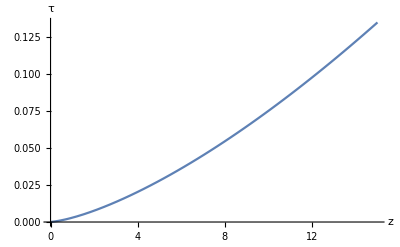

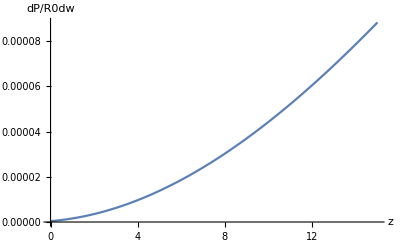

70

299800.

9802.69

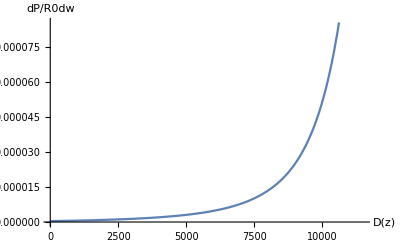

```mathematica
σ=0.665*10^-24               (*cm^2*)
n0=1.925*10^-7                 (*cm^-3*)
H0=70/(30.85*10^18)                

c=2.998*10^10                 (*cm/s*)
NIntegrate[c*σ*n0*(1+z)^2/(H0 √(0.27*(1+z)^3+0.73)),{z,0,11.33}]
Plot[NIntegrate[c*σ*n0*(1+z)^2/(H0*√(0.27*(1+z)^3+0.73)),{z,0,x}],{x,0,15}, AxesLabel->{z,τ}]
Plot[30.85*10^23*Exp[-NIntegrate[c*σ*n0*(1+z)^2/(H0*√(0.27*(1+z)^3+0.73)),{z,0,x}]]*(1+x)^2*σ*n0,{x,0,15},AxesLabel->{"z","dP/R0dw"}]
H00=70
c00=2.998*10^5
d[z_]:=NIntegrate[c00/(H00*√(0.27*(1+z0)^3+0.73)),{z0,0,z}]
d[10]
Z[dd_]:=z/.Quiet@FindRoot[d[z]==dd,{z,0}]
F[x_]:=30.85*10^23*Exp[-NIntegrate[c*σ*n0*(1+z)^2/(H0*√(0.27*(1+z)^3+0.73)),{z,0,x}]]*(1+x)^2*σ*n0
Plot[F@Z[dd],{dd,0,11500},AxesLabel->{"D(z)","dP/R0dw"}]
```